# Monkeypox Parameter Optimization

## Initializing Data

```mathematica
Import["/Users/wagner.palacio/Documents/Projeto/Repos/SystemModeling/Projects/Monkeypox/SEIQREpidemiologyModel.m"];
Import["https://raw.githubusercontent.com/antononcube/SystemModeling/master/Projects/Coronavirus-propagation-dynamics/WL/EpidemiologyModelModifications.m"];
Import["https://raw.githubusercontent.com/antononcube/SystemModeling/master/Projects/Coronavirus-propagation-dynamics/WL/EpidemiologyModelingVisualizationFunctions.m"];
Import["https://raw.githubusercontent.com/antononcube/SystemModeling/master/WL/SystemDynamicsInteractiveInterfacesFunctions.m"];
$PlotTheme = "Scientific";
```

Importing from GitHub:  EpidemiologyModels.m

```mathematica
cievsPEData := Import["https://raw.githubusercontent.com/palaciowagner/SystemModeling/master/Projects/Monkeypox/data/Pernambuco/Monkeypox%20-%20Pernambuco.csv", 
   "Dataset", "HeaderLines" -> 1];
owdPEData := Import["https://raw.githubusercontent.com/palaciowagner/SystemModeling/master/Projects/Monkeypox/data/OWD/latest_deprecated.csv", "Dataset", "HeaderLines" -> 1];
```

```mathematica
dateFormat = {"Day", "/", "Month", "/", "Year"};
PEdataMap = cievsPEData // Normal;
owdPEDataMap = Query[Select[StringContainsQ[ #Country, "Brazil"] && StringContainsQ[#Location, "Pernambuco"] && StringContainsQ[#Status, "confirmed"]&]] @ owdPEData;
```

```mathematica
pernambucoPopulation = QuantityMagnitude[9674793]; 
recifePopulation =  QuantityMagnitude[1661017]; 
maleInfected = 82.6/100;(*Cievs/PE. Dados atualizados em 10.11.2022, 15h.*)
estimatedInitialSusceptiblePopulation = ((recifePopulation/pernambucoPopulation)*maleInfected)*recifePopulation
```

235552.

```mathematica
groupedByDateOWD = GroupBy[Normal[owdPEDataMap], FromDateString[#"Date_confirmation", {"Year", "-", "Month", "-", "Day"}]&,Length] // Normal;
groupedCievs= Map[FromDateString[#Inicio, dateFormat]-> #"Confirmados" &,PEdataMap];
confirmadosJoined = Union[groupedByDateOWD, Take[groupedCievs, {15,-1}]] 
totalJoinedSmoothed = SmoothPeriod[Accumulate[TimeSeries[confirmadosJoined, TemporalRegularity->True]], 4, "Align"->Left];
(*SmoothPeriod[TimeSeries[Map[{FromDateString[#Inicio, dateFormat], #"Confirmados"} &,PEdataMap], TemporalRegularity -> True], 4, "Align"->Left]*)
(*totalConfirmadosOWDPE=Smooth[Accumulate[TimeSeries[groupedByDateOWD, TemporalRegularity->True]]];*)
totalConfirmadosPE = 
    SmoothPeriod[Accumulate[TimeSeries[Map[{FromDateString[#Inicio, dateFormat], #"Confirmados"} &,PEdataMap], TemporalRegularity -> True]], 4, "Align"->Left];
```

{Thu 21 Jul 2022→2,Fri 29 Jul 2022→4,Fri 5 Aug 2022→3,Sat 6 Aug 2022→3,Fri 12 Aug 2022→2,Tue 16 Aug 2022→1,Thu 18 Aug 2022→3,Wed 24 Aug 2022→4,Fri 26 Aug 2022→1,Mon 29 Aug 2022→1,Wed 31 Aug 2022→3,Thu 1 Sep 2022→14,Sun 4 Sep 2022→6,Tue 6 Sep 2022→1,Thu 8 Sep 2022→8,Fri 9 Sep 2022→4,Tue 13 Sep 2022→7,Wed 14 Sep 2022→23,Thu 15 Sep 2022→5,Fri 16 Sep 2022→12,Sat 17 Sep 2022→4,Tue 20 Sep 2022→7,Fri 23 Sep 2022→8,Tue 27 Sep 2022→2,Fri 30 Sep 2022→16,Tue 4 Oct 2022→10,Fri 7 Oct 2022→10,Tue 11 Oct 2022→0,Fri 14 Oct 2022→0,Tue 18 Oct 2022→1,Fri 21 Oct 2022→0,Tue 25 Oct 2022→3,Fri 28 Oct 2022→10,Tue 1 Nov 2022→8,Fri 4 Nov 2022→24,Tue 8 Nov 2022→3}

```mathematica
initialInfected =  Normal[totalJoinedSmoothed][[1]][[2]]
realIPData = <|"Infected"-> Ceiling[totalJoinedSmoothed["Values"]] // Normal|>
lsFocusParams = {β, α1, α2};
```

2

<|Infected→{2,6,6,11,12,14,17,18,23,24,34,48,58,84,105,122,127,136,154,164,164,164,165,167,173,186,210}|>

## Literature Data

Alguns dados que tirei de  artigos sobre a dinâmica da Monkeypox que serão uteis para as formulas

#### Periodo de Incubação

```mathematica
incubation = Range[5, 21];
incubationPeriod = Mean[incubation];
incubationPeriod
```

13

#### Período de Infecção [1]

```mathematica
prodomalPhase = Range[0, 3];
rashPhase = Range[7, 21];
infectiousPeriod = Mean[Map[Median] @ {prodomalPhase, rashPhase}]
maxInfectiousPeriod = Max[prodomalPhase, rashPhase]
medianInfectiousPeriod = Flatten[ {prodomalPhase,rashPhase}]
```

31/4

21

{0,1,2,3,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21}

#### Taxa de Recuperação (γ)

De acordo com [2], γ ==1/λ, sendo λ a média do período de infecção total.

## Otimização de parâmetros (β, α1, α2) dinâmico

### Taxa de Propagação ρT

```mathematica
(* Propagation Rate *)
ρt[t_, ζ_] := (NIP[t-5] +NIP[t-4]+ NIP[t-3])/(NIP[t-5-ζ] + NIP[t-4-ζ]+NIP[t-3-ζ])
(* Moving Average of Propagation Rate *)
(*ρT[T_,t_, ζ_]=Sum[ρt[t+i, ζ],{i,-(T-1)/2,(T-1)/2}]*1/T*)
equation = ρT'[t]== Sum[ρt[t+i, ζ],{i,-(T-1)/2,(T-1)/2}]*1/T
```

ρT'[t]==(∑_(i=(1-T)/2)^(1/2 (-1+T)) (NIP[-5+i+t]+NIP[-4+i+t]+NIP[-3+i+t])/(NIP[-5+i+t-ζ]+NIP[-4+i+t-ζ]+NIP[-3+i+t-ζ]))/T

```mathematica
nonAccumulatedInfected = SmoothPeriod[TimeSeries[confirmadosJoined, TemporalRegularity->True], 4, "Align"->Left]
infectedAsMap = Normal@nonAccumulatedInfected
points ={ToModelTime[First@First@infectedAsMap, #1], #2}& @@@ Normal[nonAccumulatedInfected] //Echo[#, "", Multicolumn]&
infectedValues = Association@Map[First@# -> Last@#&,points]
chunk = 7;
```

TimeSeries[…]

{{Thu 21 Jul 2022 00:00:00GMT-3,2},{Mon 25 Jul 2022 00:00:00GMT-3,4},{Fri 29 Jul 2022 00:00:00GMT-3,4},{Tue 2 Aug 2022 00:00:00GMT-3,3},{Sat 6 Aug 2022 00:00:00GMT-3,3},{Wed 10 Aug 2022 00:00:00GMT-3,2},{Sun 14 Aug 2022 00:00:00GMT-3,2},{Thu 18 Aug 2022 00:00:00GMT-3,3},{Mon 22 Aug 2022 00:00:00GMT-3,3},{Fri 26 Aug 2022 00:00:00GMT-3,1},{Tue 30 Aug 2022 00:00:00GMT-3,9},{Sat 3 Sep 2022 00:00:00GMT-3,4},{Wed 7 Sep 2022 00:00:00GMT-3,6},{Sun 11 Sep 2022 00:00:00GMT-3,12},{Thu 15 Sep 2022 00:00:00GMT-3,7},{Mon 19 Sep 2022 00:00:00GMT-3,8},{Fri 23 Sep 2022 00:00:00GMT-3,5},{Tue 27 Sep 2022 00:00:00GMT-3,9},{Sat 1 Oct 2022 00:00:00GMT-3,10},{Wed 5 Oct 2022 00:00:00GMT-3,10},{Sun 9 Oct 2022 00:00:00GMT-3,0},{Thu 13 Oct 2022 00:00:00GMT-3,0},{Mon 17 Oct 2022 00:00:00GMT-3,1},{Fri 21 Oct 2022 00:00:00GMT-3,2},{Tue 25 Oct 2022 00:00:00GMT-3,7},{Sat 29 Oct 2022 00:00:00GMT-3,8},{Wed 2 Nov 2022 00:00:00GMT-3,24}}

{0,2} | {20,2} | {40,9} | {60,8} | {80,0} | {100,8}
{4,4} | {24,2} | {44,4} | {64,5} | {84,0} | {104,24}
{8,4} | {28,3} | {48,6} | {68,9} | {88,1} | 
{12,3} | {32,3} | {52,12} | {72,10} | {92,2} | 
{16,3} | {36,1} | {56,7} | {76,10} | {96,7} |

{{0,2},{4,4},{8,4},{12,3},{16,3},{20,2},{24,2},{28,3},{32,3},{36,1},{40,9},{44,4},{48,6},{52,12},{56,7},{60,8},{64,5},{68,9},{72,10},{76,10},{80,0},{84,0},{88,1},{92,2},{96,7},{100,8},{104,24}}

<|0→2,4→4,8→4,12→3,16→3,20→2,24→2,28→3,32→3,36→1,40→9,44→4,48→6,52→12,56→7,60→8,64→5,68→9,72→10,76→10,80→0,84→0,88→1,92→2,96→7,100→8,104→24|>

```mathematica
initial = <|T->chunk,ζ->13|> 

rateRules ={
NIP'[t]== Indexed[ls,t],
NIP[t /; t<0]==0,
NIP[t /; Mod[t,T]==0]== Indexed[ls,(t/T)+1],
NIP[t /; Mod[t,T]!=0]== Indexed[ls,(t - Floor[Mod[t,T]] // TraditionalForm)+1]
}
```

<|T→7,ζ→13|>

{NIP'[t]==lst,NIP[t/;t<0]==0,NIP[t/;Mod[t,T]==0]==ls1+t/T,NIP[t/;Mod[t,T]≠0]==ls1+(t-Floor[tT])}

```mathematica
propagationEquation = Flatten@{equation ,rateRules} //. initial
```

{ρT'[t]==1/7 ((NIP[-8+t]+NIP[-7+t]+NIP[-6+t])/(NIP[-21+t]+NIP[-20+t]+NIP[-19+t])+(NIP[-7+t]+NIP[-6+t]+NIP[-5+t])/(NIP[-20+t]+NIP[-19+t]+NIP[-18+t])+(NIP[-6+t]+NIP[-5+t]+NIP[-4+t])/(NIP[-19+t]+NIP[-18+t]+NIP[-17+t])+(NIP[-5+t]+NIP[-4+t]+NIP[-3+t])/(NIP[-18+t]+NIP[-17+t]+NIP[-16+t])+(NIP[-4+t]+NIP[-3+t]+NIP[-2+t])/(NIP[-17+t]+NIP[-16+t]+NIP[-15+t])+(NIP[-3+t]+NIP[-2+t]+NIP[-1+t])/(NIP[-16+t]+NIP[-15+t]+NIP[-14+t])+(NIP[-2+t]+NIP[-1+t]+NIP[t])/(NIP[-15+t]+NIP[-14+t]+NIP[-13+t])),NIP'[t]==lst,NIP[t/;t<0]==0,NIP[t/;Mod[t,7]==0]==ls1+t/7,NIP[t/;Mod[t,7]≠0]==ls1+(t-Floor[t7])}

```mathematica
propagationSolution = Association @ Flatten@ParametricNDSolve[propagationEquation,{ρT,NIP},{t, 0, 27},{ls}, Method->Automatic]
```

<|ρT→ParametricFunction[<>],NIP→ParametricFunction[<>]|>

```mathematica
params = propagationSolution[[1]]["Parameters"] //. <|ls->Map[Last,infectedValues]|>;
f=propagationSolution[[2]][Sequence@@params];
ts = Range@@ {0,100,1};
Transpose[{ts, f[ts]}]
```

Last::normal: Nonatomic expression expected at position 1 in Last[2].

Last::normal: Nonatomic expression expected at position 1 in Last[4].

General::stop: Further output of Last::normal will be suppressed during this calculation.

ParametricNDSolve::prange: Invalid non-numeric value <|0→Last[2],4→Last[4],8→Last[4],12→Last[3],16→Last[3],20→Last[2],24→Last[2],28→Last[3],32→Last[3],36→Last[1],40→Last[9],44→Last[4],48→Last[6],52→Last[12],56→Last[7],60→Last[8],64→Last[5],68→Last[9],72→Last[10],76→Last[10],80→Last[0],84→Last[0],88→Last[1],92→Last[2],96→Last[7],100→Last[8],104→Last[24]|> for parameter ls.

Transpose::nmtx: The first two levels of {{0,1,2,3,4,5,6,7,8,9,«91»},ParametricFunction[1,Internal`Bag[<1>],2,1,False,{{ls$16387},«5»,{0}},{NDSolve`base$16397,NDSolve`NDSolveParametricFunction[0,{ParametricNDSolve,Internal`Bag[<2>],None,ParametricNDSolve},{{{2,0,0,2,0,0,0,1,0},{0,0,0,0,0,0,0,0,0}},{0,{«1»&,«1»&,«1»&},{0,{«1»}},{{«2»},{«2»},{«2»}}},None,{{{«1»},System`Utilities`HashTable[<2>],{},{},{«1»},{«3»},{«1»}},{Automatic},None,{}}},{ρT,NIP},«4»,{Cache→True,CacheTableLength→19,CacheTableWidth→7,CacheKeyMaxBytes→1000000,CacheResultMaxBytes→1000000,KeyComparison→None,ResultComparison→LessEqual},{},«1»]}][<|«1»|>][{0,«9»,«91»}]} cannot be transposed.

Transpose[{{0,1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57,58,59,60,61,62,63,64,65,66,67,68,69,70,71,72,73,74,75,76,77,78,79,80,81,82,83,84,85,86,87,88,89,90,91,92,93,94,95,96,97,98,99,100},ParametricFunction[<>][<|0→Last[2],4→Last[4],8→Last[4],12→Last[3],16→Last[3],20→Last[2],24→Last[2],28→Last[3],32→Last[3],36→Last[1],40→Last[9],44→Last[4],48→Last[6],52→Last[12],56→Last[7],60→Last[8],64→Last[5],68→Last[9],72→Last[10],76→Last[10],80→Last[0],84→Last[0],88→Last[1],92→Last[2],96→Last[7],100→Last[8],104→Last[24]|>][{0,1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57,58,59,60,61,62,63,64,65,66,67,68,69,70,71,72,73,74,75,76,77,78,79,80,81,82,83,84,85,86,87,88,89,90,91,92,93,94,95,96,97,98,99,100}]}]

```mathematica
Map[ParametricFunctionValues[#,<|α->1|>, 100]&, propagationSolution]
```

Transpose::nmtx: The first two levels of {{0,1,2,3,4,5,6,7,8,9,«91»},ParametricFunction[1,Internal`Bag[<1>],1,1,False,{{ls$16387},«5»,{0}},{NDSolve`base$16397,NDSolve`NDSolveParametricFunction[0,{ParametricNDSolve,Internal`Bag[<2>],None,ParametricNDSolve},{{{2,0,0,2,0,0,0,1,0},{0,0,0,0,0,0,0,0,0}},{0,{«1»&,«1»&,«1»&},{0,{«1»}},{{«2»},{«2»},{«2»}}},None,{{{«1»},System`Utilities`HashTable[<2>],{},{},{«1»},{«3»},{«1»}},{Automatic},None,{}}},{ρT,NIP},«4»,{Cache→True,CacheTableLength→19,CacheTableWidth→7,CacheKeyMaxBytes→1000000,CacheResultMaxBytes→1000000,KeyComparison→None,ResultComparison→LessEqual},{},«1»]}][ls][{0,1,«8»,«91»}]} cannot be transposed.

Transpose::nmtx: The first two levels of {{0,1,2,3,4,5,6,7,8,9,«91»},ParametricFunction[1,Internal`Bag[<1>],2,1,False,{{ls$16387},«5»,{0}},{NDSolve`base$16397,NDSolve`NDSolveParametricFunction[0,{ParametricNDSolve,Internal`Bag[<2>],None,ParametricNDSolve},{{{2,0,0,2,0,0,0,1,0},{0,0,0,0,0,0,0,0,0}},{0,{«1»&,«1»&,«1»&},{0,{«1»}},{{«2»},{«2»},{«2»}}},None,{{{«1»},System`Utilities`HashTable[<2>],{},{},{«1»},{«3»},{«1»}},{Automatic},None,{}}},{ρT,NIP},«4»,{Cache→True,CacheTableLength→19,CacheTableWidth→7,CacheKeyMaxBytes→1000000,CacheResultMaxBytes→1000000,KeyComparison→None,ResultComparison→LessEqual},{},«1»]}][ls][{0,1,«8»,«91»}]} cannot be transposed.

<|ρT→Transpose[{{0,1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57,58,59,60,61,62,63,64,65,66,67,68,69,70,71,72,73,74,75,76,77,78,79,80,81,82,83,84,85,86,87,88,89,90,91,92,93,94,95,96,97,98,99,100},ParametricFunction[<>][ls][{0,1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57,58,59,60,61,62,63,64,65,66,67,68,69,70,71,72,73,74,75,76,77,78,79,80,81,82,83,84,85,86,87,88,89,90,91,92,93,94,95,96,97,98,99,100}]}],NIP→Transpose[{{0,1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57,58,59,60,61,62,63,64,65,66,67,68,69,70,71,72,73,74,75,76,77,78,79,80,81,82,83,84,85,86,87,88,89,90,91,92,93,94,95,96,97,98,99,100},ParametricFunction[<>][ls][{0,1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57,58,59,60,61,62,63,64,65,66,67,68,69,70,71,72,73,74,75,76,77,78,79,80,81,82,83,84,85,86,87,88,89,90,91,92,93,94,95,96,97,98,99,100}]}]|>

### Definição do Modelo

```mathematica
ClearAll[modelSEIQRDynamicBeta];
modelSEIQRDynamicBeta = With[{contactRate=ToExpression["Global`"<>"β"]},
model = SEIQRModel[t, "InitialConditions" -> True, "RateRules" -> True, 
   "TotalPopulationRepresentation" -> "Constant"];
(*lsRepRules={
contactRate -> contactRate[t]
};
(*model["Rates"] = KeyDrop[model["Rates"], {contactRate}];*)
model["Rates"]=KeyMap[#/. lsRepRules&,model["Rates"]];
model["Equations"]=Map[#/. lsRepRules&,model["Equations"]];
model["RateRules"]=Association[Normal[model["RateRules"]]/. lsRepRules];
model["RateRules"]=KeyDrop[model["RateRules"],{contactRate[t]}];*)
(*AppendTo[model["Stocks"],NIP[t]->"Newly Infected Population"];
AppendTo[model["Stocks"],PR[t]->"Propagation Rate"];*)model["InitialConditions"]=ReplacePart[model["InitialConditions"],3-> IP[t /; t<=0]==initialInfected];
(*AppendTo[modelSEIQRDynamicBeta["InitialConditions"], NIP[t/; IP[-1+t]+IP[t]===0]==1];*)
(*AppendTo[model["InitialConditions"], NIP[t /; t<=0]==1];
AppendTo[model["InitialConditions"], PR[t /; t<=0]==0];
AppendTo[model["Equations"], NIP'[t]==IP[t]-IP[t-1]];
AppendTo[model["Equations"], PR'[t]==ρT[7,t, ζ] ];*)
(*AppendTo[model["Equations"], ρ'[T]==((ρ[t-6] + ρ[t-5] +ρ[t-4] + ρ[t-3]+ ρ[t-2]+ρ[t])/T ];*)

(*AppendTo[model["InitialConditions"],  β[t /; t<=0]==0.001];*)
model];
```

```mathematica
modelSEIQRDynamicBeta = SetRateRules[modelSEIQRDynamicBeta, 
<|NP[0] -> Round[estimatedInitialSusceptiblePopulation/100],
λ-> infectiousPeriod,
ζ->incubationPeriod|>
];
modelSEIQRDynamicBeta = SetInitialConditions[modelSEIQRDynamicBeta,
   <|
SP[0] ->  Round[estimatedInitialSusceptiblePopulation/100],
EP[0] -> 2,
QP[0] -> 8
    |>];
```

```mathematica
lsActualEquationsDynamicBeta = Join[modelSEIQRDynamicBeta["Equations"]//.KeyDrop[modelSEIQRDynamicBeta["RateRules"], lsFocusParams],modelSEIQRDynamicBeta["InitialConditions"]]
ModelGridTableForm[modelSEIQRDynamicBeta]
```

{SP'[t]==0.2 QP[t]-(β IP[t] SP[t])/2356,EP'[t]==-((α1+α2) EP[t])+(β IP[t] SP[t])/2356,IP'[t]==α1 EP[t]-(4 IP[t])/31,QP'[t]==α2 EP[t]-0.329032 QP[t],RP'[t]==(4 IP[t])/31+(4 QP[t])/31,SP[0]==2356,EP[0]==2,IP[t/;t≤0]==2,QP[0]==8,RP[0]==0}

<|Stocks→# | Symbol | Description
1 | NP[t] | Total Population
2 | SP[t] | Susceptible Population
3 | EP[t] | Exposed Population
4 | IP[t] | Infected Population
5 | QP[t] | Quarantined Population
6 | RP[t] | Recovered Population,Rates→# | Symbol | Description
1 | β | Contact rate for the infected population
2 | α1 | Proportion of Exposed to Infected Rate (Confirmed)
3 | α2 | Proportion Sent to Quarantine (Suspected)
4 | φ | Proportion of not detected after medical diagnosis (Discarded)
5 | τ | Proportion from Suspected to Recovered class
6 | γ | Recovery Rate
7 | ζ | Average Incubation Period
8 | λ | Average Infection Period,Equations→# | Equation
1 | SP'[t]==φ QP[t]-(β IP[t] SP[t])/NP[0]
2 | EP'[t]==-((α1+α2) EP[t])+(β IP[t] SP[t])/NP[0]
3 | IP'[t]==α1 EP[t]-γ IP[t]
4 | QP'[t]==α2 EP[t]-(τ+φ) QP[t]
5 | RP'[t]==γ IP[t]+τ QP[t],RateRules→# | Symbol | Value
1 | NP[0] | 2356
2 | β | 6.×10^-6
3 | α1 | 1/ζ
4 | α2 | 1/ζ
5 | φ | 0.2
6 | τ | γ
7 | γ | 1/λ
8 | ζ | 13
9 | λ | 31/4,InitialConditions→# | Equation
1 | SP[0]==2356
2 | EP[0]==2
3 | IP[t/;t≤0]==2
4 | QP[0]==8
5 | RP[0]==0|>

```mathematica
asolDynamicBeta = Association @ Flatten@ParametricNDSolve[lsActualEquationsDynamicBeta,{SP,EP,IP,QP, RP},{t,0,100},lsFocusParams, Method->Automatic,MaxStepSize->1, StartingStepSize->1]
```

<|SP→ParametricFunction[<>],EP→ParametricFunction[<>],IP→ParametricFunction[<>],QP→ParametricFunction[<>],RP→ParametricFunction[<>]|>

```mathematica
ResourceFunction["GridTableForm"][List /@ lsActualEquationsDynamicBeta]
```

# | 1
1 | SP'[t]==0.2 QP[t]-(β IP[t] SP[t])/2356
2 | EP'[t]==-((α1+α2) EP[t])+(β IP[t] SP[t])/2356
3 | IP'[t]==α1 EP[t]-(4 IP[t])/31
4 | QP'[t]==α2 EP[t]-0.329032 QP[t]
5 | RP'[t]==(4 IP[t])/31+(4 QP[t])/31
6 | SP[0]==2356
7 | EP[0]==2
8 | IP[t/;t≤0]==2
9 | QP[0]==8
10 | RP[0]==0

```mathematica
allValues =Map[ParametricFunctionValues[#,<|β->0.517,α1->0.729,α2->0.692|>, {0,100,1}]&, asolDynamicBeta]
```

<|SP→{{0,2356.},{1,2356.2},{2,2355.86},{3,2355.1},{4,2353.99},{5,2352.55},{6,2350.81},{7,2348.76},{8,2346.39},{9,2343.68},{10,2340.62},{11,2337.15},{12,2333.26},{13,2328.89},{14,2324.},{15,2318.53},{16,2312.41},{17,2305.59},{18,2297.98},{19,2289.51},{20,2280.09},{21,2269.63},{22,2258.04},{23,2245.2},{24,2231.02},{25,2215.39},{26,2198.19},{27,2179.32},{28,2158.66},{29,2136.11},{30,2111.58},{31,2084.99},{32,2056.28},{33,2025.38},{34,1992.3},{35,1957.02},{36,1919.59},{37,1880.09},{38,1838.63},{39,1795.35},{40,1750.44},{41,1704.11},{42,1656.63},{43,1608.26},{44,1559.3},{45,1510.05},{46,1460.81},{47,1411.9},{48,1363.58},{49,1316.13},{50,1269.79},{51,1224.77},{52,1181.23},{53,1139.33},{54,1099.16},{55,1060.81},{56,1024.32},{57,989.706},{58,956.967},{59,926.078},{60,896.997},{61,869.672},{62,844.039},{63,820.028},{64,797.564},{65,776.569},{66,756.964},{67,738.671},{68,721.612},{69,705.711},{70,690.897},{71,677.099},{72,664.252},{73,652.291},{74,641.158},{75,630.796},{76,621.152},{77,612.178},{78,603.827},{79,596.056},{80,588.824},{81,582.094},{82,575.831},{83,570.003},{84,564.579},{85,559.53},{86,554.831},{87,550.458},{88,546.387},{89,542.597},{90,539.069},{91,535.785},{92,532.728},{93,529.881},{94,527.231},{95,524.763},{96,522.465},{97,520.325},{98,518.333},{99,516.478},{100,514.75}},EP→{{0,2.},{1,1.17698},{2,1.11984},{3,1.21933},{4,1.36173},{5,1.52712},{6,1.71345},{7,1.92224},{8,2.15587},{9,2.4171},{10,2.70898},{11,3.03486},{12,3.39836},{13,3.80343},{14,4.25432},{15,4.75559},{16,5.31209},{17,5.92893},{18,6.61147},{19,7.3652},{20,8.19575},{21,9.10868},{22,10.1094},{23,11.2031},{24,12.3942},{25,13.6865},{26,15.0827},{27,16.584},{28,18.1898},{29,19.8975},{30,21.7018},{31,23.5943},{32,25.5635},{33,27.5943},{34,29.6679},{35,31.7616},{36,33.8495},{37,35.9024},{38,37.8887},{39,39.7754},{40,41.5288},{41,43.1164},{42,44.5075},{43,45.6752},{44,46.5973},{45,47.2574},{46,47.6455},{47,47.7588},{48,47.6009},{49,47.1823},{50,46.5189},{51,45.6316},{52,44.545},{53,43.2857},{54,41.8822},{55,40.3625},{56,38.7544},{57,37.0838},{58,35.3747},{59,33.6486},{60,31.9244},{61,30.2181},{62,28.5432},{63,26.9108},{64,25.3294},{65,23.8056},{66,22.3441},{67,20.948},{68,19.6192},{69,18.3583},{70,17.165},{71,16.0385},{72,14.9771},{73,13.9788},{74,13.0414},{75,12.1624},{76,11.339},{77,10.5685},{78,9.8481},{79,9.17511},{80,8.54677},{81,7.96045},{82,7.41359},{83,6.90372},{84,6.42851},{85,5.98572},{86,5.57322},{87,5.18903},{88,4.83124},{89,4.4981},{90,4.18792},{91,3.89915},{92,3.63032},{93,3.38007},{94,3.14712},{95,2.93027},{96,2.72842},{97,2.54052},{98,2.36562},{99,2.2028},{100,2.05123}},IP→{{0,2.},{1,2.75353},{2,3.18856},{3,3.59935},{4,4.04578},{5,4.54394},{6,5.10218},{7,5.728},{8,6.42939},{9,7.21514},{10,8.09496},{11,9.07957},{12,10.1808},{13,11.4116},{14,12.7862},{15,14.3201},{16,16.0302},{17,17.9346},{18,20.053},{19,22.4064},{20,25.0168},{21,27.9078},{22,31.1035},{23,34.629},{24,38.5095},{25,42.77},{26,47.4348},{27,52.5265},{28,58.0652},{29,64.0675},{30,70.5453},{31,77.5043},{32,84.9427},{33,92.85},{34,101.205},{35,109.975},{36,119.115},{37,128.567},{38,138.256},{39,148.099},{40,157.995},{41,167.837},{42,177.506},{43,186.879},{44,195.832},{45,204.24},{46,211.988},{47,218.967},{48,225.084},{49,230.26},{50,234.437},{51,237.575},{52,239.655},{53,240.679},{54,240.665},{55,239.651},{56,237.688},{57,234.839},{58,231.178},{59,226.784},{60,221.741},{61,216.135},{62,210.05},{63,203.572},{64,196.778},{65,189.745},{66,182.542},{67,175.235},{68,167.881},{69,160.532},{70,153.234},{71,146.027},{72,138.944},{73,132.015},{74,125.264},{75,118.709},{76,112.367},{77,106.247},{78,100.359},{79,94.7077},{80,89.2961},{81,84.1247},{82,79.1922},{83,74.4958},{84,70.0315},{85,65.7941},{86,61.7774},{87,57.9749},{88,54.3793},{89,50.9829},{90,47.778},{91,44.7564},{92,41.9102},{93,39.2312},{94,36.7115},{95,34.3432},{96,32.1186},{97,30.0301},{98,28.0705},{99,26.2329},{100,24.5102}},QP→{{0,8.},{1,6.60783},{2,5.41714},{3,4.58625},{4,4.06234},{5,3.77674},{6,3.67522},{7,3.71891},{8,3.88108},{9,4.14398},{10,4.49659},{11,4.93285},{12,5.45046},{13,6.05002},{14,6.73438},{15,7.50817},{16,8.37752},{17,9.34978},{18,10.4333},{19,11.6374},{20,12.972},{21,14.4475},{22,16.0747},{23,17.8644},{24,19.8273},{25,21.9735},{26,24.3122},{27,26.8512},{28,29.5962},{29,32.5503},{30,35.7135},{31,39.0817},{32,42.6459},{33,46.3921},{34,50.2997},{35,54.3419},{36,58.4849},{37,62.6881},{38,66.9042},{39,71.0802},{40,75.158},{41,79.0765},{42,82.7727},{43,86.1847},{44,89.2531},{45,91.9241},{46,94.1513},{47,95.8973},{48,97.1359},{49,97.8524},{50,98.0441},{51,97.7201},{52,96.9005},{53,95.6149},{54,93.9009},{55,91.8024},{56,89.3673},{57,86.646},{58,83.6896},{59,80.548},{60,77.269},{61,73.8976},{62,70.4744},{63,67.0361},{64,63.6148},{65,60.2378},{66,56.9283},{67,53.7051},{68,50.5833},{69,47.5743},{70,44.6865},{71,41.9256},{72,39.2948},{73,36.7955},{74,34.4273},{75,32.1887},{76,30.0768},{77,28.088},{78,26.2183},{79,24.4629},{80,22.8168},{81,21.2749},{82,19.832},{83,18.4828},{84,17.2222},{85,16.0449},{86,14.9462},{87,13.9212},{88,12.9653},{89,12.0742},{90,11.2437},{91,10.4699},{92,9.74905},{93,9.07763},{94,8.45233},{95,7.87006},{96,7.32789},{97,6.82309},{98,6.35312},{99,5.91558},{100,5.50824}},RP→{{0,0.},{1,1.25711},{2,2.41342},{3,3.49282},{4,4.54062},{5,5.59769},{6,6.69837},{7,7.87196},{8,9.14461},{9,10.5407},{10,12.0839},{11,13.7982},{12,15.7085},{13,17.8412},{14,20.2246},{15,22.8894},{16,25.8694},{17,29.201},{18,32.9245},{19,37.0837},{20,41.7266},{21,46.9054},{22,52.6767},{23,59.1016},{24,66.2461},{25,74.1805},{26,82.9797},{27,92.7228},{28,103.492},{29,115.374},{30,128.456},{31,142.825},{32,158.571},{33,175.779},{34,194.531},{35,214.901},{36,236.956},{37,260.749},{38,286.323},{39,313.699},{40,342.883},{41,373.858},{42,406.585},{43,441.002},{44,477.021},{45,514.532},{46,553.403},{47,593.482},{48,634.599},{49,676.572},{50,719.208},{51,762.307},{52,805.669},{53,849.094},{54,892.391},{55,935.374},{56,977.872},{57,1019.73},{58,1060.79},{59,1100.94},{60,1140.07},{61,1178.08},{62,1214.89},{63,1250.45},{64,1284.71},{65,1317.64},{66,1349.22},{67,1379.44},{68,1408.31},{69,1435.82},{70,1462.02},{71,1486.91},{72,1510.53},{73,1532.92},{74,1554.11},{75,1574.14},{76,1593.07},{77,1610.92},{78,1627.75},{79,1643.6},{80,1658.52},{81,1672.55},{82,1685.73},{83,1698.11},{84,1709.74},{85,1720.65},{86,1730.87},{87,1740.46},{88,1749.44},{89,1757.85},{90,1765.72},{91,1773.09},{92,1779.98},{93,1786.43},{94,1792.46},{95,1798.09},{96,1803.36},{97,1808.28},{98,1812.88},{99,1817.17},{100,1821.18}}|>

```mathematica
(*positions = Flatten@Values@ PositionIndex @ Keys[ modelSEIQRDynamicBeta["Stocks"]];
First@positions*)
```

```mathematica
(*({#[20]})& /@ asolDynamicBeta *)
```

```mathematica
opts={PlotRange->All,PlotLegends->None,PlotTheme->"Detailed",PerformanceGoal->"Speed",ImageSize->800};
Manipulate[
DynamicModule[{lsPopulationPlots2},
lsPopulationPlots2=
Quiet[ParametricSolutionsPlots[
modelSEIQRDynamicBeta["Stocks"],
KeyTake[asolDynamicBeta,GetPopulationSymbols[modelSEIQRDynamicBeta, __ ~~ "Population"]],{contactRate, alpha1, alpha2},nWeeks,"Together"->popTogetherQ,opts]];
  Show[lsPopulationPlots2[[3]],ListPlot[PadRealData[realIPData,Round[incubationPeriod+padOffset],Round[infectionPeriod+padOffset]],PlotStyle->{Blue,Black,Red}]]
  (*Multicolumn[plots, nPlotColumns, Dividers -> All, 
   FrameStyle -> GrayLevel[0.8]]*)
],
{{population,estimatedInitialSusceptiblePopulation/100,"Population"},100,estimatedInitialSusceptiblePopulation,50,Appearance->{"Open"}},
{{padOffset,0,"real data padding offset"},-100,100,1,Appearance->{"Open"}},
{{contactRate, 0.540, StringJoin["Contact rate of the infected population (β)", ToString[DisplayForm[InterpretationBox[SuperscriptBox["10", "-4"], var]]]]}, 0.001, 1, 0.001, 
  Appearance -> {"Open"}},
 {{incubationPeriod, 13, "Incubation period (ζ) in days "}, 5, 21, 1, 
  Appearance -> {"Open"}},
 {{alpha1, 0.718, "Alpha 1(α1)"}, 0, 1, 0.001, 
  Appearance -> {"Open"}},
 {{alpha2, 0.693, "Alpha 2(α2)"}, 0, 1, 0.001, 
  Appearance -> {"Open"}},
 {{infectionPeriod,7, "Infection period (λ) in days "}, 0, 21, 1, 
  Appearance -> {"Open"}},
 {{nWeeks,28, "Epidemiological Week (t)"}, 1, 52, 1, Appearance -> {"Open"}},
 {{nPlotColumns, 1, "Number of plot columns"}, Range[3]}, 
{{popTogetherQ, False, "Plot populations together"}, {False, True}},
ControlPlacement->Left,ContinuousAction->False]
```

## Simulações

```mathematica
totalNewlyInfectedOptimizedDynamic = SmoothPeriod[Accumulate[TimeSeries[confirmadosJoined, TemporalRegularity->True]],7, "Align"-> Left] // Normal
```

{{Thu 21 Jul 2022 00:00:00GMT-3,2},{Thu 28 Jul 2022 00:00:00GMT-3,6},{Thu 4 Aug 2022 00:00:00GMT-3,11},{Thu 11 Aug 2022 00:00:00GMT-3,16},{Thu 18 Aug 2022 00:00:00GMT-3,20},{Thu 25 Aug 2022 00:00:00GMT-3,29},{Thu 1 Sep 2022 00:00:00GMT-3,48},{Thu 8 Sep 2022 00:00:00GMT-3,74},{Thu 15 Sep 2022 00:00:00GMT-3,108},{Thu 22 Sep 2022 00:00:00GMT-3,127},{Thu 29 Sep 2022 00:00:00GMT-3,149},{Thu 6 Oct 2022 00:00:00GMT-3,164},{Thu 13 Oct 2022 00:00:00GMT-3,165},{Thu 20 Oct 2022 00:00:00GMT-3,167},{Thu 27 Oct 2022 00:00:00GMT-3,182}}

```mathematica
(*totalSusceptibleOptimized = SmoothPeriod[Accumulate[TimeSeries[expostosJoined, TemporalRegularity->True]],maxInfectiousPeriod] // Normal*)
firstDateInfectedDynamic = First @ First@Normal[totalNewlyInfectedOptimizedDynamic];
lastDateInfectedDynamic = First @  Last@ Normal[totalNewlyInfectedOptimizedDynamic];
fitInfectedDataDynamic={ToModelTime[firstDateInfectedDynamic, #1], #2}& @@@ Normal[totalNewlyInfectedOptimizedDynamic] //Echo[#, "", Multicolumn]&;
```

{0,2} | {28,20} | {56,108} | {84,165}
{7,6} | {35,29} | {63,127} | {91,167}
{14,11} | {42,48} | {70,149} | {98,182}
{21,16} | {49,74} | {77,164} |

```mathematica
newlyInfectedSol =  Association@Flatten@Quiet[ParametricNDSolve[lsActualEquationsDynamicBeta,{SP,EP,IP,QP, RP},{t,0,100},lsFocusParams,MaxStepSize->1, StartingStepSize->1]];
{infectedSolDynamic, betaSolDynamic}= {IP[β,α1,α2], PR[β,α1,α2]} /.newlyInfectedSol;
currentDynamic = Take[totalNewlyInfectedOptimizedDynamic,15]
```

{{Thu 21 Jul 2022 00:00:00GMT-3,2},{Thu 28 Jul 2022 00:00:00GMT-3,6},{Thu 4 Aug 2022 00:00:00GMT-3,11},{Thu 11 Aug 2022 00:00:00GMT-3,16},{Thu 18 Aug 2022 00:00:00GMT-3,20},{Thu 25 Aug 2022 00:00:00GMT-3,29},{Thu 1 Sep 2022 00:00:00GMT-3,48},{Thu 8 Sep 2022 00:00:00GMT-3,74},{Thu 15 Sep 2022 00:00:00GMT-3,108},{Thu 22 Sep 2022 00:00:00GMT-3,127},{Thu 29 Sep 2022 00:00:00GMT-3,149},{Thu 6 Oct 2022 00:00:00GMT-3,164},{Thu 13 Oct 2022 00:00:00GMT-3,165},{Thu 20 Oct 2022 00:00:00GMT-3,167},{Thu 27 Oct 2022 00:00:00GMT-3,182}}

```mathematica
all = {ToModelTime[First@First@Normal[currentDynamic], #1], #2}& @@@ Normal[currentDynamic]
s01 = Take[all,4]
s02=Take[all,{4,7}]
s03=Take[all,{7,10}]
s04=Take[all,{10,13}]
s05=Take[all,-3]
```

{{0,2},{7,6},{14,11},{21,16},{28,20},{35,29},{42,48},{49,74},{56,108},{63,127},{70,149},{77,164},{84,165},{91,167},{98,182}}

{{0,2},{7,6},{14,11},{21,16}}

{{21,16},{28,20},{35,29},{42,48}}

{{42,48},{49,74},{56,108},{63,127}}

{{63,127},{70,149},{77,164},{84,165}}

{{84,165},{91,167},{98,182}}

### Simulação 1

```mathematica
(*{{β,0.517}, {α1,0.729},{α2,0.692}*)
```

```mathematica
(*GetFittingModelFor := Block[{data, beta, alpha1, alpha2},*)AbsoluteTiming[fitInfectedDynamic=NonlinearModelFit[s01,{infectedSolDynamic[t], {0<β && 0<α1<=1 && 0< α2<=1}},{{β,0.517}, {α1,0.729},{α2,0.692}},t, AccuracyGoal-> 3, WorkingPrecision-> 3,  PrecisionGoal -> 3, EvaluationMonitor:> Print["β=", β,"  .α1=",α1,"   .α2=",α2],Method-> {NMinimize, Method->{"NelderMead", "PostProcess"-> {"FindMinimum"}}}]]
(*fitInfectedDynamic=NonlinearModelFit[{ToModelTime[First@First@Normal[currentDynamic], #1], #2}& @@@ Normal[currentDynamic],{infectedSolDynamic[t], α1>0&&α2 >0&&β>0},{{β,2.5},{α1,0.03},{α2,0.02}},t, AccuracyGoal-> 3, WorkingPrecision-> 6,  PrecisionGoal -> 3, EvaluationMonitor:>Print["t=", t, ".    β=", β, ".    α1=", α1, ".    α2=", α2], Method->  {NMinimize,Method->{"DifferentialEvolution","ScalingFactor"->0.9,"CrossProbability"->0.1,"PostProcess"->{FindMinimum,Method->"QuasiNewton"}}}]*)
(*GetFittingModelFor[s01,0.517,0.729,  0.692]*)
```

```mathematica
Quiet @ fitInfectedDynamic["ParameterTable"]
Quiet @ fitInfectedDynamic["BestFitParameters"]
Quiet @fitInfectedDynamic["RSquared"]
Quiet @fitInfectedDynamic["AdjustedRSquared"]
Quiet @FitWithDataPlot[fitInfectedDynamic,{First@First@Normal[currentDynamic],First@Last@Normal[currentDynamic]} ]
```

### Simulação 2

```mathematica
resultsS01 =Map[ParametricFunctionValues[#,<|β->0.231,α1->0.812,α2->N[4.49*10^-8]|>, {0,21,1}]&, asolDynamicBeta];
s01AsMap = Map[Last[Last[Last[#]]]&,Normal@resultsS01]
```

```mathematica
Total[Take[s01AsMap,5]]
```

```mathematica
(*modelSEIQRDynamicBetaS02 = SetRateRules[modelSEIQRDynamicBetaS02, <|NP[0] -> N[Total[Take[s01AsMap,5]]] |>];
modelSEIQRDynamicBetaS02 = SetInitialConditions[modelSEIQRDynamicBetaS02,
   <|
SP[21] ->  First@s01AsMap,
EP[21] -> s01AsMap[[2]],
IP[21] ->s01AsMap[[3]],
QP[21] ->s01AsMap[[4]],
RP[21] ->s01AsMap[[5]],
NIP[21] ->s01AsMap[[6]],
PR[21] ->s01AsMap[[7]],
    |>]*)
```

```mathematica
AbsoluteTiming[fitInfectedDynamic02=NonlinearModelFit[s02,{infectedSolDynamic[t], {0<β && 0<α1<=1 && 0< α2<=1}},{{β,0.231}, {α1,0.812},{α2,N[4.49*10^-8]}},t, AccuracyGoal-> 3, WorkingPrecision-> 3,  PrecisionGoal -> 3, EvaluationMonitor:> Print["β=", β,"  .α1=",α1,"   .α2=",α2],Method-> {NMinimize, Method->{"NelderMead", "PostProcess"-> {"FindMinimum"}}}]]
```

```mathematica
Quiet @ fitInfectedDynamic02["ParameterTable"]
Quiet @ fitInfectedDynamic02["BestFitParameters"]
Quiet @fitInfectedDynamic02["RSquared"]
Quiet @fitInfectedDynamic02["AdjustedRSquared"]
Quiet @FitWithDataPlot[fitInfectedDynamic02,{First@First@Normal[currentDynamic],First@Last@Normal[currentDynamic]} ]
```

```mathematica
Association@Quiet @ fitInfectedDynamic02["BestFitParameters"]
```

### Simulação 3

```mathematica
AbsoluteTiming[fitInfectedDynamic03=NonlinearModelFit[s03,{infectedSolDynamic[t], {0<β && 0<α1<=1 && 0< α2<=1}},{{β,0.217}, {α1,0.803},{α2,0.0170}},t, AccuracyGoal-> 3, WorkingPrecision-> 3,  PrecisionGoal -> 3, EvaluationMonitor:> Print["β=", β,"  .α1=",α1,"   .α2=",α2],Method-> {NMinimize, Method->{"NelderMead", "PostProcess"-> {"FindMinimum"}}}]]
```

```mathematica
Quiet @ fitInfectedDynamic03["ParameterTable"]
Quiet @ fitInfectedDynamic03["BestFitParameters"]
Quiet @fitInfectedDynamic03["RSquared"]
Quiet @fitInfectedDynamic03["AdjustedRSquared"]
Quiet @FitWithDataPlot[fitInfectedDynamic03,{First@First@Normal[currentDynamic],First@Last@Normal[currentDynamic]} ]
```

### Simulação 4

```mathematica
AbsoluteTiming[fitInfectedDynamic04=NonlinearModelFit[s04,{infectedSolDynamic[t], {0<β && 0<α1<=1 && 0< α2<=1}},{{β,0.356}, {α1,0.999},{α2,0.686}},t, AccuracyGoal-> 3, WorkingPrecision-> 3,  PrecisionGoal -> 3, EvaluationMonitor:> Print["β=", β,"  .α1=",α1,"   .α2=",α2],Method-> {NMinimize, Method->{"NelderMead", "PostProcess"-> {"FindMinimum"}}}]]
```

```mathematica
Quiet @ fitInfectedDynamic04["ParameterTable"]
Quiet @ fitInfectedDynamic04["BestFitParameters"]
Quiet @fitInfectedDynamic04["RSquared"]
Quiet @fitInfectedDynamic04["AdjustedRSquared"]
Quiet @FitWithDataPlot[fitInfectedDynamic04,{First@First@Normal[currentDynamic],First@Last@Normal[currentDynamic]} ]
```

### Simulação 5

```mathematica
AbsoluteTiming[fitInfectedDynamic05=NonlinearModelFit[s05,{infectedSolDynamic[t], {0<β && 0<α1<=1 && 0< α2<=1}},{{β,0.354}, {α1,0.377},{α2,0.216}},t, AccuracyGoal-> 3, WorkingPrecision-> 3,  PrecisionGoal -> 3, EvaluationMonitor:> Print["β=", β,"  .α1=",α1,"   .α2=",α2],Method-> {NMinimize, Method->{"NelderMead", "PostProcess"-> {"FindMinimum"}}}]]
```

```mathematica
Quiet @ fitInfectedDynamic05["ParameterTable"]
Quiet @ fitInfectedDynamic05["BestFitParameters"]
Quiet @fitInfectedDynamic05["RSquared"]
Quiet @fitInfectedDynamic05["AdjustedRSquared"]
Quiet @FitWithDataPlot[fitInfectedDynamic05,{First@First@Normal[currentDynamic],First@Last@Normal[currentDynamic]} ]
```

### Simulação Total

```mathematica
AbsoluteTiming[fitInfectedDynamicAll=NonlinearModelFit[all,{infectedSolDynamic[t], {0<β && 0<α1<=1 && 0< α2<=1}},{{β,0.517}, {α1,0.729},{α2,0.692}},t, AccuracyGoal-> 3, WorkingPrecision-> 3,  PrecisionGoal -> 3, EvaluationMonitor:> Print["β=", β,"  .α1=",α1,"   .α2=",α2],Method-> {NMinimize, Method->{"NelderMead", "PostProcess"-> {"FindMinimum"}}}]]
```

```mathematica
Quiet @ fitInfectedDynamicAll["ParameterTable"]
Quiet @ fitInfectedDynamicAll["BestFitParameters"]
Quiet @fitInfectedDynamicAll["RSquared"]
Quiet @fitInfectedDynamicAll["AdjustedRSquared"]
Quiet @FitWithDataPlot[fitInfectedDynamicAll,{First@First@Normal[currentDynamic],First@Last@Normal[currentDynamic]} ]
```

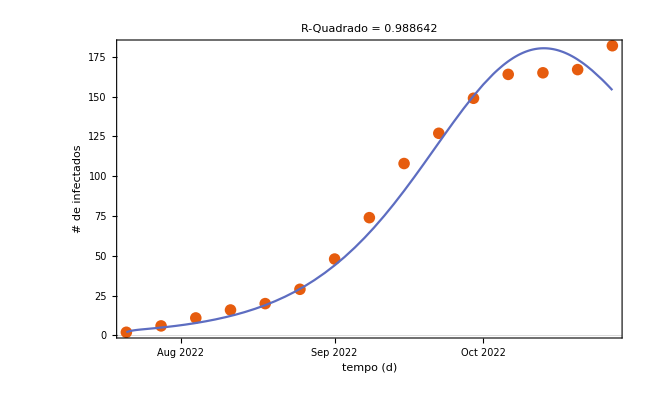

```mathematica
00001.260604874863131`3*10^-4
```

```mathematica
RealDigits[0.0001260604874863131`3.]
```

```mathematica
Chunk[list_,chunk_]:=Flatten[Partition[list,chunk][[#;;;;2]]]&/@{1,2}
```

```mathematica
fits ={fitInfectedDynamic, fitInfectedDynamic02, fitInfectedDynamic03, fitInfectedDynamic04, fitInfectedDynamic05}
```

```mathematica
JoinFittedDatePlot[fits_List,fitComplete_FittedModel,{dateMin_DateObject,dateMax_DateObject}]:=
Module[{plotAll,plotData,bands,cd, chunks},
cd=ColorData[108];
firstFit = First@fits;
lastFit = Last@fits;
plotAll={ToDataDate[dateMin,#1],#2}&@@@fitComplete["Data"];
plotData=Map[{ToDataDate[dateMin,#1],#2}&@@@#["Data"]&,fits];
bands[x_]=Quiet @ fitComplete["SinglePredictionBands",ConfidenceLevel->0.95]&/. t->x;
Show[DateListPlot[plotAll,Joined->True,PlotRange->All],
DateListPlot[plotData,Joined->False,PlotRange->All,PlotTheme->"Detailed"],
Plot[{fitComplete[ToModelTime[dateMin,FromAbsoluteTime@t]]&,
bands[ToModelTime[dateMin,FromAbsoluteTime@t]]},
{t,AbsoluteTime@dateMin,AbsoluteTime@dateMax},
PlotRange->All,
PlotStyle->{cd[2],None},
Filling->{2->{1}},
FillingStyle->{Opacity[0.5,Lighter@cd[2]]},
Exclusions->None],
PlotRange->All,
PlotRangePadding->{Automatic,{Scaled[0.03],Scaled[0.1]}},
FrameLabel->{"tempo (d)","# de infectados"},ImageSize->360,
PlotLabel->StringForm["Simulações com parâmetros ajustados"]]
//Labeled[#,Column[{LineLegend[{cd[1]},{"S00"}],PointLegend[{cd[2]},{"S01"}],PointLegend[{cd[3]},{"S02"}],PointLegend[{cd[4]},{"S03"}],PointLegend[{cd[5]},{"S04"}], PointLegend[{cd[6]},{"S05"}]},Left],Right]&]
```

```mathematica
JoinFittedDatePlot[fits,fitInfectedDynamicAll, {First@First@Normal[currentDynamic],First@Last@Normal[currentDynamic]}]
```

```mathematica
dateMin = First@First@Normal[currentDynamic];
dateMax = First@Last@Normal[currentDynamic];
bands[x_,t_]=Quiet @ Map[#["SinglePredictionBands",ConfidenceLevel->0.95]&/. t->x, fits]
```

## Modelo Final

```mathematica
(*lastFit = fitInfectedDynamic05 ;
lastParameters = Association@fitInfectedDynamic04["BestFitParameters"]*)
(*Normal@lastParameters[[2]]*)
(*lastFit["Data"]*)
lastParameters=<|β->0.332, α1->0.160, α2->0.053|>
resultsLastSimulation =Map[ParametricFunctionValues[#,<|β->0.332, α1->0.160, α2->0.053|>, {84,98,1}]&, asolDynamicBeta]
resultsLastSimulationMap = Map[Last[Last[Last[#]]]&,Normal@resultsLastSimulation]
```

<|β→0.332,α1→0.16,α2→0.053|>

<|SP→{{84,1454.66},{85,1426.53},{86,1398.52},{87,1370.7},{88,1343.1},{89,1315.78},{90,1288.8},{91,1262.19},{92,1236.01},{93,1210.28},{94,1185.05},{95,1160.35},{96,1136.2},{97,1112.64},{98,1089.68}},EP→{{84,148.041},{85,149.128},{86,149.944},{87,150.483},{88,150.744},{89,150.727},{90,150.433},{91,149.865},{92,149.031},{93,147.938},{94,146.596},{95,145.015},{96,143.208},{97,141.188},{98,138.971}},IP→{{84,159.785},{85,162.751},{86,165.5},{87,168.018},{88,170.291},{89,172.307},{90,174.054},{91,175.525},{92,176.712},{93,177.611},{94,178.217},{95,178.53},{96,178.55},{97,178.28},{98,177.724}},QP→{{84,22.908},{85,23.198},{86,23.4493},{87,23.6604},{88,23.8301},{89,23.9573},{90,24.0415},{91,24.0823},{92,24.0796},{93,24.0338},{94,23.9455},{95,23.8156},{96,23.6453},{97,23.436},{98,23.1894}},RP→{{84,582.606},{85,606.392},{86,630.582},{87,655.142},{88,680.035},{89,705.225},{90,730.671},{91,756.333},{92,782.168},{93,808.136},{94,834.191},{95,860.292},{96,886.395},{97,912.457},{98,938.437}}|>

{1089.68,138.971,177.724,23.1894,938.437}

```mathematica
modelSEIQRFinal = SetRateRules[modelSEIQRDynamicBeta, <|
NP[99] -> SP[98]+EP[98]+IP[98]+QP[98]+RP[98],  
β->Normal@lastParameters[[1]],
α1-> Normal@lastParameters[[2]],
α2->Normal@lastParameters[[3]]|>];
modelSEIQRFinal = SetInitialConditions[modelSEIQRFinal,
   <|
SP[98] -> resultsLastSimulationMap[[1]],
EP[98] -> resultsLastSimulationMap[[2]],
IP[98] -> resultsLastSimulationMap[[3]],
QP[98] -> resultsLastSimulationMap[[4]],
RP[98] -> resultsLastSimulationMap[[5]]
    |>]; (* Subtrair do número da primeira semana epidemiológica*)
lsActualEquationsFinal = Join[modelSEIQRFinal["Equations"] //. KeyDrop[modelSEIQRFinal["RateRules"], {}], modelSEIQRFinal["InitialConditions"]]
ModelGridTableForm[modelSEIQRFinal]
ResourceFunction["GridTableForm"][List /@ lsActualEquationsFinal]
aSolFinal = NDSolve[lsActualEquationsFinal,{SP,EP,IP,QP, RP},{t,99,161}]
```

{SP'[t]==0.2 QP[t]-0.000140917 IP[t] SP[t],EP'[t]==-0.213 EP[t]+0.000140917 IP[t] SP[t],IP'[t]==0.16 EP[t]-(4 IP[t])/31,QP'[t]==0.053 EP[t]-0.329032 QP[t],RP'[t]==(4 IP[t])/31+(4 QP[t])/31,SP[0]==2356,EP[0]==2,IP[t/;t≤0]==2,QP[0]==8,RP[0]==0}

<|Stocks→# | Symbol | Description
1 | NP[t] | Total Population
2 | SP[t] | Susceptible Population
3 | EP[t] | Exposed Population
4 | IP[t] | Infected Population
5 | QP[t] | Quarantined Population
6 | RP[t] | Recovered Population,Rates→# | Symbol | Description
1 | β | Contact rate for the infected population
2 | α1 | Proportion of Exposed to Infected Rate (Confirmed)
3 | α2 | Proportion Sent to Quarantine (Suspected)
4 | φ | Proportion of not detected after medical diagnosis (Discarded)
5 | τ | Proportion from Suspected to Recovered class
6 | γ | Recovery Rate
7 | ζ | Average Incubation Period
8 | λ | Average Infection Period,Equations→# | Equation
1 | SP'[t]==φ QP[t]-(β IP[t] SP[t])/NP[0]
2 | EP'[t]==-((α1+α2) EP[t])+(β IP[t] SP[t])/NP[0]
3 | IP'[t]==α1 EP[t]-γ IP[t]
4 | QP'[t]==α2 EP[t]-(τ+φ) QP[t]
5 | RP'[t]==γ IP[t]+τ QP[t],RateRules→# | Symbol | Value
1 | NP[0] | 2356
2 | β | 0.332
3 | α1 | 0.16
4 | α2 | 0.053
5 | φ | 0.2
6 | τ | γ
7 | γ | 1/λ
8 | ζ | 13
9 | λ | 31/4
10 | NP[99] | EP[98]+IP[98]+QP[98]+RP[98]+SP[98],InitialConditions→# | Equation
1 | SP[0]==2356
2 | EP[0]==2
3 | IP[t/;t≤0]==2
4 | QP[0]==8
5 | RP[0]==0|>

# | 1
1 | SP'[t]==0.2 QP[t]-0.000140917 IP[t] SP[t]
2 | EP'[t]==-0.213 EP[t]+0.000140917 IP[t] SP[t]
3 | IP'[t]==0.16 EP[t]-(4 IP[t])/31
4 | QP'[t]==0.053 EP[t]-0.329032 QP[t]
5 | RP'[t]==(4 IP[t])/31+(4 QP[t])/31
6 | SP[0]==2356
7 | EP[0]==2
8 | IP[t/;t≤0]==2
9 | QP[0]==8
10 | RP[0]==0

{{SP→InterpolatingFunction[…],EP→InterpolatingFunction[…],IP→InterpolatingFunction[…],QP→InterpolatingFunction[…],RP→InterpolatingFunction[…]}}

```mathematica
aSolForPeaks = Association@Flatten@ParametricNDSolve[lsActualEquationsFinal,{SP,EP,IP,QP, RP},{t,99,161},{β,α1,α2}]
```

<|SP→ParametricFunction[<>],EP→ParametricFunction[<>],IP→ParametricFunction[<>],QP→ParametricFunction[<>],RP→ParametricFunction[<>]|>

```mathematica
allValues =Map[ParametricFunctionValues[#,lastParameters, {99,161,1}]&, aSolForPeaks];
peaks = Map[FindPeaks[Last/@#]&,allValues]
```

<|SP→{{1,1067.34}},EP→{{1,136.572}},IP→{{1,176.889}},QP→{{1,22.9075}},RP→{{63,1763.43}}|>

```mathematica
Clear[PadRealData];
PadRealData[aData:Association[(_String->_?VectorQ)..],incubationPeriod_?IntegerQ,infectiousPeriod_?IntegerQ]:=Block[{},Join[ConstantArray[0,incubationPeriod+infectiousPeriod],#]&/@aData];
```

```mathematica
optsFinal={"LogPlot"->True,PlotRange->All,PlotLegends->None,PlotTheme->"Detailed",PerformanceGoal->"Speed",ImageSize->800};
DynamicModule[{beta=Normal@lastParameters[[1]],alpha1=Normal@lastParameters[[2]],alpha2=Normal@lastParameters[[3]],nWeeks=161,padOffset=-7},
DynamicModule[{modelSEIQR=modelSEIQRFinal,lsFinal},
lsFinal = ParametricSolutionsPlots[modelSEIQR["Stocks"],#,{beta,alpha1,alpha2},nWeeks,"Together"->True,optsFinal]&/@GroupBy[Normal@aSolFinal,#[[1,1]]&,Association];
(*Show[List@Plot[Map[Identity[#]&,Values[aSolFinal]],{t,0,100}, PlotRange->All,PlotLegends->None,PlotTheme->"Detailed"], ListPlot[peaks,PlotStyle-> {Red,Black,Blue}]]]]*)
Show[lsFinal[[1,1]], ListPlot[Labeled[#,#]&/@peaks, PlotLabels->Above,PlotLegends->None]]
]
]
```

## Sensibilidade de parâmetro

```mathematica
ResidualsPlot[fitInfectedDynamic05]
```

```mathematica
ClearAll[modelSensitivityPlot]
modelSensitivityPlot[modelIn:(_ParametricFunction[__]),fit_FittedModel,{{tMin_?NumberQ,tMax_?NumberQ},{yMin_?NumberQ,yMax_?NumberQ}},scale:{__?NumberQ}]:=Module[{model,sensitivities,cd=ColorData[108],params,t},params=fit["BestFitParameters"];
model=modelIn[t]/. params;
sensitivities=MapThread[model+(#2 {-1,1} D[modelIn,#1][t]/. params)&,{Keys@params,scale}];
TabView@MapThread[Function[{p,bands,sf},p->(Show[ListPlot[fit["Data"],PlotRange->All],Plot[{model,bands}//Evaluate,{t,tMin,tMax},PlotRange->All,PlotStyle->{cd[2],Lighter@cd[3],Lighter@cd[4]},Filling->{2->{{1},Opacity[0.5,Lighter@cd[3]]},3->{{1},Opacity[0.5,Lighter@cd[4]]}}],PlotRange->{All,{yMin,yMax}},PlotRangePadding->{Automatic,{Scaled[0.03],Scaled[0.1]}},FrameLabel->{"tempo (t) dias","# de infectados"},PlotLabel->"Sensibilidade do parâmetro",Epilog->{Inset[StringForm["Fator de Escala = ``",TraditionalForm[sf]],Scaled[{0.05,0.95}],{-1,1}]}]//Labeled[#,Column[{PointLegend[{cd[1]},{"Observado"}],LineLegend[{cd[2]},{"Calculado"}],SwatchLegend[{Opacity[0.5,Lighter@cd[3]]},{"Sensibilidade Negativa"}],SwatchLegend[{Opacity[0.5,Lighter@cd[4]]},{"Sensibilidade Positiva"}]},Left],Right]&)],{Keys@params,sensitivities,scale}]]
```

```mathematica
modelSensitivityPlot[infectedSolDynamic,fitInfectedDynamic05,{{0,100},{-10,190}},{0.354, 0.377,0.216}]
```